```mathematica
(** Various helper functions for standard parts of the paper / reachable set results **)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
cmat[ab_, tau_, tf_] := MatrixExp[-(tau - tf) ab // Transpose][[4;;6, 1;;3]];
xrf[tf_, delta_, h_, deltaT_, A_, n_, Rr_] := NIntegrate[  h n^2 Rr (cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta / (deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt)[[1]]  ,{tau, 0, tf}];
x3fanalytical[tf_, h_, n_]:= h(2Floor[n tf / Pi]+1+ Mod[Floor[n tf / Pi], 2] Cos[n tf] - (Mod[Floor[n tf / Pi], 2] - 1)(- Cos[n tf]));
```

```mathematica
(** Computes the thrust-limited reachable set for a given final time **)
thrustreachable[xrf_,tf_] := Module[{points, tfs, hs, As, ns, Rrs, pointsT, rd, rdpoints, rdboundary, first2},
points = CirclePoints[1000];
points = Append[#, 0] & /@ points;
points //  N;
points[[1]];
tfs = ConstantArray[tf, 1000];
tfs[[1]];
hs = ConstantArray[100, 1000];
hs[[1]];
As = ConstantArray[CW[5], 1000];
As[[1]] // MatrixForm;
ns = ConstantArray[5, 1000];
ns[[1]];
Rrs = ConstantArray[1, 1000];
Rrs[[1]];
columntorow[x_] := {x};
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;
rd = MapThread[xrf, {tfs, points, hs, pointsT, As, ns, Rrs}];
rdpoints = Map[Re, rd, {2}];
rdboundary = PolygonCoordinates[ConvexHullRegion[rdpoints]];
first2[x_] := {x[[1]], x[[2]]};
rboundary = Map[first2, rdboundary];
rboundary
]
bounds = thrustreachable[xrf, 1];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(** There seems to be symmetry causing me to select just one value **)
(** reachable set as linear transformation of unit circle **) 
reachablestatsoperator[b_, points_] := Module[{rats, vecs}, 
ratio[k_, a_]:= 1 / Norm[(a // Inverse).k];
maxminrat[a_, v1s_] := {MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max,   MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min };
maxminvec[a_, v1s_] := {v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max    ][[1, 1]] ]], v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min    ][[1, 1]] ]]};
rats = maxminrat[b, points];
vecs = maxminvec[b, points];
{rats, vecs}
]
stats = reachablestatsoperator[{{100, 0}, {0, 1000}}, bounds]
```

{{0.376019,0.076118},{{47.8573,2616.02},{-1267.28,3463.18}}}

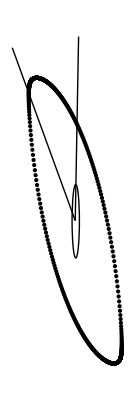

Show::gtype: Out is not a type of graphics.

```mathematica
vectoangle[k_] := ArcTan[k[[1]],k[[2]]]
Show[{Graphics[Point[bounds]], Graphics[Circle[{0, 0}, {100, 1000}]], Graphics[Line[5000 AnglePath[{vecs[[1]] // vectoangle}]]], Graphics[Line[5000AnglePath[{vecs[[2]] // vectoangle}]]]}]
```